### Conditions: 2 t_1 t_2 t_3=1 and r_2=r_1 t_2

(1-t_2^2)=r_1^2 t_2^2
1/((1+r_1^2)^(1/2))=t_2=1/((2-t_1^2)^(1/2))

2 t_1 1/((2-t_1^2)^(1/2))t_3=1
4 t_1^2/(2-t_1^2)t_3=1

```mathematica
t1[t3_]=√(2/(4 t3^2+1))
```

√2 √(1/(1+4 t3^2))

```mathematica
t2 [t3_]= 1/(√(2-t1[t3]^2))
```

1/(√(2-2/(1+4 t3^2)))

```mathematica
t3=N[1/2]
```

0.5

```mathematica
{t1[1/(√2)],t2[1/√2]}
```

{√(2/3),(√3)/2}

```mathematica
√(1-3/4)
```

1/2

```mathematica
N[1/(2 √2)]
```

0.353553

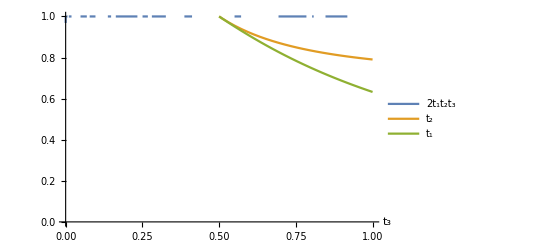

```mathematica
Plot[{2 t1[t3] t2[t3] t3,t2[t3],t1[t3]},{t3,0,1},PlotRange->{0,1},PlotLegends->Placed[{"2t_1t_2t_3","t_2","t_1"},{0.25,0.5}],AxesLabel->{"t_3"},LabelStyle->Large]
```

```mathematica
N[1/√2]
```

0.707107

```mathematica
FindMaximum[{√((1-t2[t3]^2)(1-t3^2)),0≤ t3≤1},{t3,0.6}]
```

{0.353553,{t3→0.707107}}

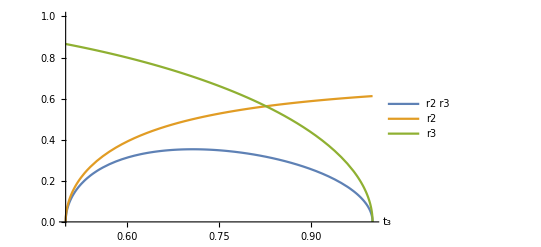

```mathematica
Plot[{√((1-t2[t3]^2)(1-t3^2)),√(1-t2[t3]^2),√(1-t3^2)},{t3,0.5,1},PlotRange->{0,1},PlotLegends->Placed[{r2 r3,r2,r3},{0.9,.65}],GridLines->{{1/√2},{√((1-t2[1/√2]^2)(1-1/2))}},LabelStyle->Medium,AxesLabel->{Subscript[t, 3]}]
```

## C-π/2

```mathematica
ClearAll[α,γ,ϕ,t2,t3]
PD[α_,γ_,ϕ_,t2_,t3_]=0.18082(1-t2^2)(1-t3^2)(1+2(α^2 Re[γ √(1-γ^2)ⅇ^(ⅈ ϕ)]+(1-α^2)Re[ⅈ γ √(1-γ^2)ⅇ^(ⅈ ϕ)]));
```

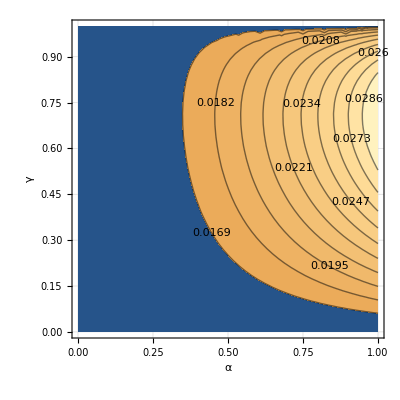

```mathematica
ContourPlot[  PD[α,γ,0,√(2/3),(√3)/2],{α,0,1},{γ,0,1},FrameLabel->Automatic,RotateLabel-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotRange->Full,Contours->10,ImageSize->Scaled[0.25],ColorFunctionScaling->True,ContourLabels-> All]
```

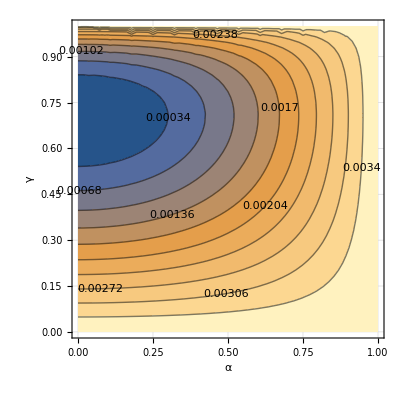

```mathematica
ContourPlot[0.25 PD[α,γ,π/2,√(2/3),(√3)/2],{α,0,1},{γ,0,1},FrameLabel->Automatic,RotateLabel-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotRange->Full,Contours->10,ImageSize->Scaled[0.25],ColorFunctionScaling->True,ContourLabels-> All]
```

## C-π

```mathematica
ClearAll[α,γ,ϕ,t2,t3]
PD[α_,γ_,ϕ_,t2_,t3_]=0.25(1-t2^2)(1-t3^2)(1+2(α^2-(1-α^2)Re[γ √(1-γ^2)ⅇ^(ⅈ ϕ)]));
```

```mathematica
Average= (∫_0^1 ∫_0^1 ∫_0^(2π) Simplify[PD[α,γ,ϕ,(√3)/2,1/√2]]ⅆϕⅆγⅆα)/(2π)
```

```mathematica
(∫_0^(2 π) (0.05208333333333333-0.013888888888888888 Cos[ϕ])ⅆϕ)/(2 π)
```

0.0520833

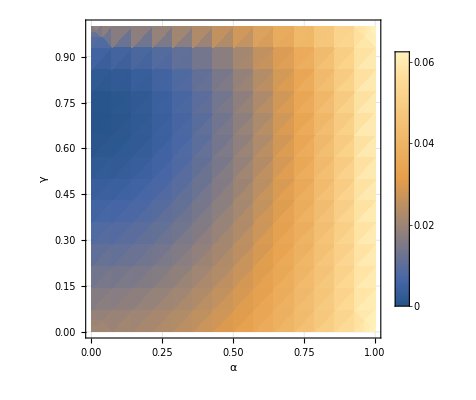

```mathematica
DensityPlot[PD[α,γ,0,√(2/3),(√3)/2],{α,0,1},{γ,0,1},FrameLabel->Automatic,RotateLabel-> True,LabelStyle->Large,AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotRange->Full,ImageSize->Scaled[0.5],ColorFunctionScaling->True,PlotLegends->Automatic]
```

```mathematica
PD[0,0.5,π/2,√(2/3),(√3)/2]
```

0.0208333

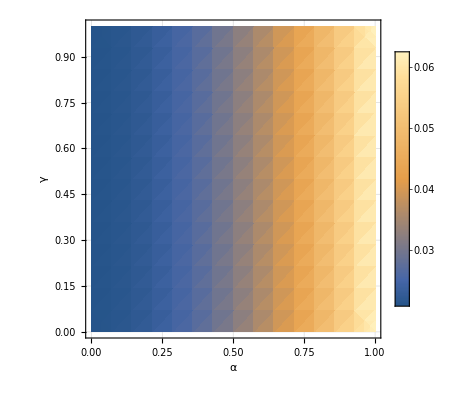

```mathematica
DensityPlot[ PD[α,γ,π/2,√(2/3),(√3)/2],{α,0,1},{γ,0,1},FrameLabel->Automatic,RotateLabel-> True,LabelStyle->Large,AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotRange->Full,ImageSize->Scaled[0.5],ColorFunctionScaling->True,PlotLegends->Automatic]
```

## Input state: weak coherent state approximated as α0+β1

```mathematica
X=π;
PNSG=0.25;
β=√(1-α^2)ⅇ^(ⅈ Subscript[ϕ, T]);
δ=√(1-γ^2)ⅇ^(ⅈ Subscript[ϕ, C]);
Subscript[ψ, T]=α +β Subscript[c, T];
Subscript[ψ, CA]=γ Subscript[c, b]+δ Subscript[c, a];
ψ=Expand[Subscript[ψ, T] Subscript[ψ, CA]];
B[t_]={{t,ⅈ √(1-t^2)},{ⅈ  √(1-t^2),t}};
Subscript[t, 1]=√(2/3);
Subscript[t, 2]=(√3)/2;
Subscript[t, 3]=1/(√2);
```

## Gate Transformation

## Modes T and a mix at the first beam splitter:

```mathematica
{Subscript[c, T],Subscript[c, a]}=B[Subscript[t, 1]].{Subscript[c, T1],Subscript[c, a1]};
```

## Nonlinear phase gate

```mathematica
{Subscript[A, 0],Subscript[A, 1],Subscript[A, 2]}=CoefficientList[Expand[ψ],Subscript[c, T1]];
ψ=Subscript[A, 0]+Subscript[A, 1] Subscript[c, T1]+ⅇ^(ⅈ X)Subscript[A, 2] Subscript[c, T1]^2;
```

## Modes T1 and b mix at the second beam splitter:

```mathematica
{Subscript[c, T1],Subscript[c, b]}=B[Subscript[t, 2]].{Subscript[c, T2],Subscript[c, b1]};
```

## Modes T2 and c mix at the third beam splitter:

```mathematica
{Subscript[c, T2],Subscript[c, c]}=B[Subscript[t, 3]].{Subscript[c, T3],Subscript[c, c1]};
```

## Inefficient detectors: Modelled as Perfect ones with beam splitter of t=√η

```mathematica
{Subscript[c, a1],Subscript[c, ad1]}=B[√η].{Subscript[c, ap],Subscript[c, ad]};
{Subscript[c, b1],Subscript[c, bd1]}=B[√η].{Subscript[c, bp],Subscript[c, bd]};
{Subscript[c, c1],Subscript[c, cd1]}=B[√η].{Subscript[c, cp],Subscript[c, cd]};
```

## Project onto the state where we have 0,0,1 photons in the modes ‘a1’, ‘b1’ and ‘c1’ respectively The ‘1’ in the labels of the modes denotes that they are outputs modes of beam splitters

```mathematica
Collect[-2 √2 FullSimplify[CoefficientList[Expand[ψ],{Subscript[c, ap],Subscript[c, bp],Subscript[c, cp]}][[1,1,2]]],{α,β}]
```

α (γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) √η+(ⅇ^(ⅈ ϕ_T) √(1-α^2) √η ((-γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) √(6-6 η) c_ad+2 (γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) √(3-3 η) c_bd+3 √2 (-γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) (√(1-η) c_cd-c_T3)))/(3 √2)

```mathematica
ClearAll[η]
```

```mathematica
α (γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) √η+(ⅇ^(ⅈ Subscript[ϕ, T]) √(1-α^2) √η ((-γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) √(6-6 η) Subscript[c, ad]+2 (γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) √(3-3 η) Subscript[c, bd]+3 √2 (-γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) (√(1-η) Subscript[c, cd]-Subscript[c, T3])))/(3 √2)
```

```mathematica
Collect[FullSimplify[CoefficientList[Expand[ψ],{Subscript[c, ap],Subscript[c, bp],Subscript[c, cp]}][[1,1,2]]],{α,β}]
```

(α (-γ-ⅇ^(ⅈ ϕ_C) √(1-γ^2)))/(2 √2)+(ⅇ^(ⅈ ϕ_T) √(1-α^2) (-γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) c_T3)/(2 √2)

```mathematica
Collect[(-γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) √(6-6 η) Subscript[c, ad]+2 (γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) √(3-3 η) Subscript[c, bd]+3 √2 (-γ+ⅇ^(ⅈ Subscript[ϕ, C]) √(1-γ^2)) (√(1-η) Subscript[c, cd]-Subscript[c, T3]),{Subscript[c, ad],Subscript[c, bd],Subscript[c, cd],Subscript[c, T]}]
```

(-γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) √(6-6 η) c_ad+2 (γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) √(3-3 η) c_bd+3 √2 (-γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) √(1-η) c_cd-3 √2 (-γ+ⅇ^(ⅈ ϕ_C) √(1-γ^2)) c_T3

```mathematica
newStyle[A_]:=A/.l_Line:>Sequence[Opacity[1],Thickness[.005],Red,l]
n=4;
ClearAll[u,v,x,y]
ContourPlot[S1[n,√n,√n,π/4,0,π,aprime,bprime],{aprime,-π,π},{bprime,-π,π},LabelStyle->{FontSize->18,FontFamily->"Times",Black},Axes-> True, FrameStyle-> {Thickness[0.000001],Gray,Opacity[0.4]},AxesLabel->{"σ'_A","σ'_B"},PlotLegends->Automatic] /.Tooltip[A_,2]:>Tooltip[newStyle[A],2]
```

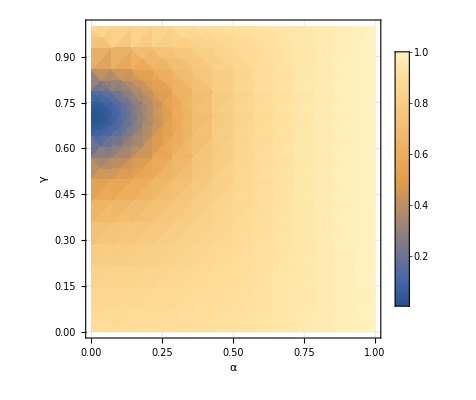

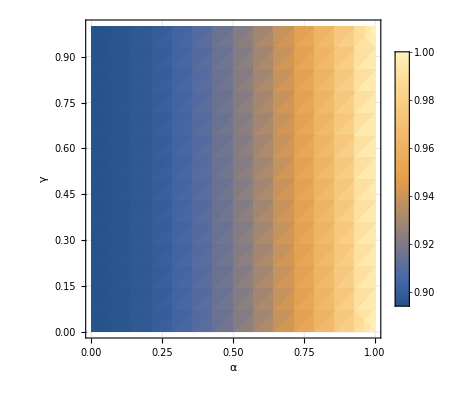

```mathematica
F[α_,γ_,ϕ_,η_]=1/(1+((1-α^2)(1-η))/16(19+10 γ √(1-γ^2)Cos[ϕ])/(1+2(α^2-(1-α^2))γ √(1-γ^2)Cos[ϕ]));
η=0.9;
newStyle[A_]:=A/.l_Line:>Sequence[Opacity[1],Thickness[.005],Red,l]
DensityPlot[ F[α,γ,0,η],{α,0,1},{γ,0,1},FrameLabel->Automatic,RotateLabel-> True,LabelStyle->Large,AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotRange->Full,ImageSize->Scaled[0.5],ColorFunctionScaling->True,PlotLegends->Automatic]
DensityPlot[ F[α,γ,π/2,η],{α,0,1},{γ,0,1},FrameLabel->Automatic,RotateLabel-> True,LabelStyle->Large,AxesStyle->Thick,GridLines->Automatic ,Axes->True, PlotRange->Full,ImageSize->Scaled[0.5],ColorFunctionScaling->True,PlotLegends->Automatic]/.Tooltip[A_,0.9]:>Tooltip[newStyle[A],0.9]
```